# Research Xor-Binary-Linear Operator.

## We are going to understand it step by step 04 June 2017

Problem description

a) v = {0,1}^N, for example if N =5 v can be equals to {0,1,1,0,0}
b) v_1+ v_2 means v_1 xor x_2
c) Let A be a generation set: A={a_i| i ∈ 1..K, 0<K≤2^N}. Generation means that using a_i we can get 2^Kvectors like (∑^K)_(i=1) β_i α_i , β_i∈{0,1}.
d) Vectors’ weight means the number of 1 inside it. 
Example: W({0,1,1,0,0}) = 5

Task: for ∀ N, A plot a histogram of vectors number by their weight.

```mathematica
𝒳or[bd1_,bd2_]:=If[bd1 ≠bd2,1,0]
({#,𝒳or[#]/.List->Sequence})&/@Tuples[{0,1},2]//MatrixForm
```

({0,0} | 0
{0,1} | 1
{1,0} | 1
{1,1} | 0)

```mathematica
v1={0,0,1,1,0}
v2={1,1,1,0,1}
MapThread[𝒳or,{v1,v2}]
```

{0,0,1,1,0}

{1,1,1,0,1}

{1,1,0,1,1}

## Generation Set Let A be a generation set:

```mathematica
A={
{0,0,1,1,0},
{1,0,1,0,1},
{1,1,0,0,0}
};
```

```mathematica
B=Tuples[{0,1},A//Length]
ArrayPlot@A
ArrayPlot@B
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

-Graphics-

-Graphics-

## Call to generation set action.

```mathematica
Combines Subscript[a, i]∈ A in all possible ways B we get  all possibles vectors  for A(genA) :
```

```mathematica
B[[-2]]
genElem=MapThread[Times,{A,B[[-1]]}]
```

{1,1,0}

{{0,0,1,1,0},{1,0,1,0,1},{1,1,0,0,0}}

```mathematica
𝒳orVec=MapThread[𝒳or,{#1,#2}]&;
𝒳orVec[genElem[[1]],genElem[[2]]]
𝒳orVec[𝒳orVec[genElem[[1]],genElem[[2]] ],genElem[[3]] ]
(* it's Fold mechanics... *)
Fold[𝒳orVec]@genElem
```

{1,0,0,1,1}

{0,1,0,1,1}

{0,1,0,1,1}

```mathematica
𝒳orVec=MapThread[𝒳or,{#1,#2}]&;
fTimes=MapThread[Times, {#1,#2}]&;
genA=Fold[𝒳orVec]/@((fTimes[A,#]&)/@B)//Union
ArrayPlot@genA
```

{{0,0,0,0,0},{0,0,1,1,0},{0,1,0,1,1},{0,1,1,0,1},{1,0,0,1,1},{1,0,1,0,1},{1,1,0,0,0},{1,1,1,1,0}}

-Graphics-

Weight calculation
Lets calculate weights of each vector in genA.

```mathematica
𝒲=Total;
weights = 𝒲/@genA
```

{0,2,3,3,3,3,2,4}

Now we have to plot the weights histogram.

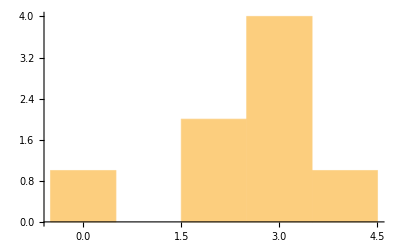

```mathematica
Histogram@weights
```

Ok, we solve the task for generation set A and N, where N=5 and A is:

```mathematica
A//MatrixForm
```

(0 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0)

## Generation set in wide

Lets generate more complex generations sets and see what happens.

```mathematica
A=RandomChoice[{0,1},{13,10}]
ArrayPlot@A
```

{{1,1,1,1,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0},{1,0,1,0,1,1,0,0,1,0},{1,1,1,1,0,1,0,0,0,1},{1,0,0,0,0,0,0,1,1,0},{1,1,0,0,1,0,1,0,1,0},{1,0,0,1,1,1,1,0,1,0},{1,0,1,1,1,1,0,0,1,0},{0,1,1,1,1,0,1,0,0,1},{0,0,0,0,0,0,1,1,1,0},{0,1,1,1,1,1,1,1,0,1},{1,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,1}}

-Graphics-

{1.4343,Null}

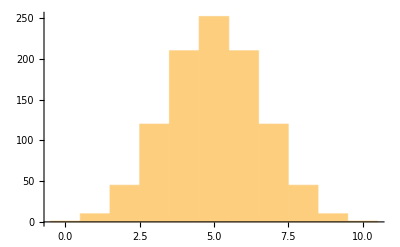

```mathematica
B=Tuples[{0,1},A//Length];
AbsoluteTiming[
genA=Fold[𝒳orVec]/@((fTimes[A,#]&)/@B)//Union;
weights = 𝒲/@genA;
]
Histogram@weights
```

Hm, Its took about 1.4 seconds to calculate the weights. Optimise it!

```mathematica
Optimization with Digits' Xor operation
```

```mathematica
AD=FromDigits[#,2]&/@A
```

{968,8,690,977,518,810,634,754,489,14,509,672,19}

```mathematica
𝒲D=DigitCount[#,2,1]&;
AbsoluteTiming[
genAD=Fold[BitXor]/@((Times[AD,#]&)/@B)//Union;
weightsD = 𝒲D/@genAD;
]
```

{0.0935052,Null}

```mathematica
Histogram@weightsD
```

-Graphics-

```mathematica
weights==weightsD
```

True

Fine! We make increase computation speed up to 10x-20x using digit XOR operator.

```mathematica
The only One function
```

```mathematica
A
```

{{1,1,1,1,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0},{1,0,1,0,1,1,0,0,1,0},{1,1,1,1,0,1,0,0,0,1},{1,0,0,0,0,0,0,1,1,0},{1,1,0,0,1,0,1,0,1,0},{1,0,0,1,1,1,1,0,1,0},{1,0,1,1,1,1,0,0,1,0},{0,1,1,1,1,0,1,0,0,1},{0,0,0,0,0,0,1,1,1,0},{0,1,1,1,1,1,1,1,0,1},{1,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,1}}

```mathematica
computeW[a_]:=Module[{ad,b,genAD,weights},
ad=FromDigits[#,2]&/@a;
b=Tuples[{0,1},a//Length];
genAD=Fold[BitXor]/@((Times[ad,#]&)/@b)//Union;
weights= 𝒲D/@genAD;
weights//Tally
]
```

```mathematica
w=computeW[A]
```

{{0,1},{1,10},{2,45},{3,120},{4,210},{5,252},{6,210},{7,120},{8,45},{9,10},{10,1}}

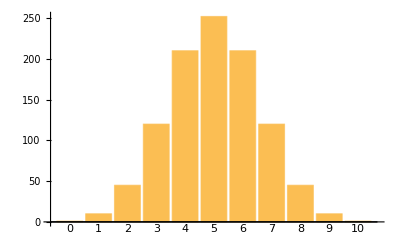

```mathematica
weightsHistorgram = BarChart[#[[;;, 2]], ChartLabels->#[[;;,1]]]&;
weightsHistorgram@w
```

Now we have one computeW function for solving our task.

```mathematica
Touch the propability
```

```mathematica
w
```

{{0,1},{1,10},{2,45},{3,120},{4,210},{5,252},{6,210},{7,120},{8,45},{9,10},{10,1}}

```mathematica
Transpose[{{0,1},{1,10},{2,45},{3,120},{4,210},{5,252},{6,210},{7,120},{8,45},{9,10},{10,1}}]
```

{{0,1,2,3,4,5,6,7,8,9,10},{1,10,45,120,210,252,210,120,45,10,1}}

```mathematica
UnTally=Fold[Join][(PadLeft[{},#[[2]],#[[1]]])&/@#]&;
```

```mathematica
wAll=UnTally [w];
wAll[[;;400]]
```

{0,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
pDistrib = EstimatedDistribution[wAll,NormalDistribution[α,β]]
```

NormalDistribution[5.,1.58114]

```mathematica
Plot estimated Normal Distribution
```

Let check the normal distribution likeness.

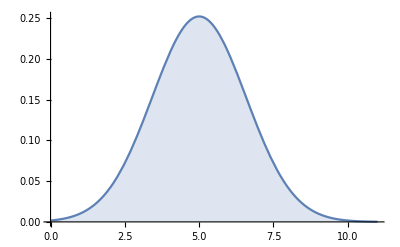

4.32956×10^-8

```mathematica
Plot[PDF[pDistrib,x]//Evaluate,{x,0,Length@w},Filling->Axis]
DistributionFitTest[wAll,pDistrib]
```

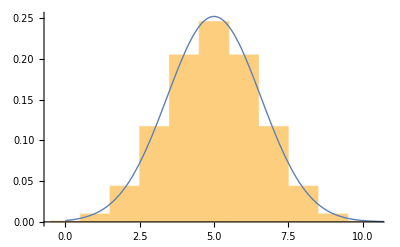

```mathematica
Show[Histogram[wAll,Automatic,"ProbabilityDensity"],Plot[PDF[pDistrib,x],{x,0,Length@w},PlotStyle->Thick]]
```

```mathematica
weightsDistribHistorgram[w_]:= Module[{wAll,pDistrib},
wAll=UnTally [w];
pDistrib = EstimatedDistribution[wAll,NormalDistribution[α,β]];
Show[Histogram[wAll,Automatic,"ProbabilityDensity"],Plot[PDF[pDistrib,x],{x,0,Max@wAll},PlotStyle->Thick]]
];
```

```mathematica
Increase zeros or ones in generation set
```

ToPValue replaced original v with v2 with p probability.

```mathematica
ToPValue[v_,v2_:0,p_:0.5]:=If[Random[]≤ p,v2,v]
```

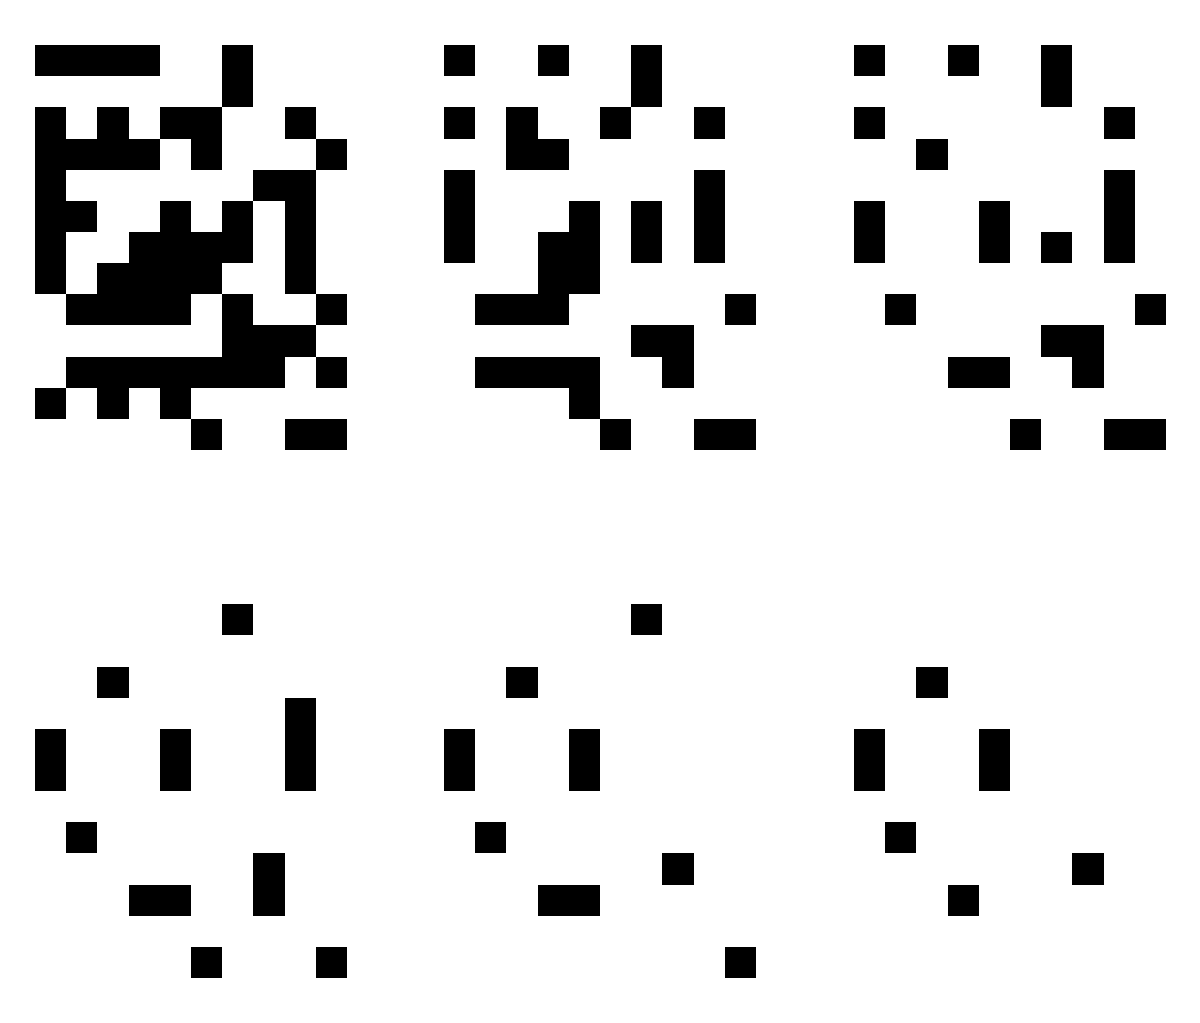

```mathematica
ANew=NestList[Map[ToPValue[#,0,0.3]&,#,{2}]&,A,5];
GraphicsGrid[Partition[ArrayPlot/@ANew,3]]
```

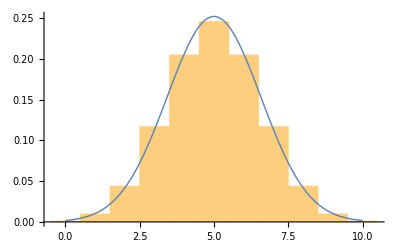
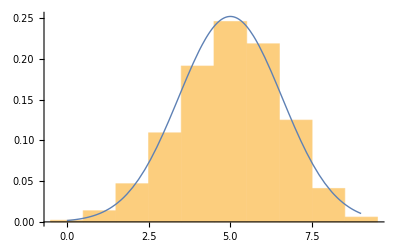
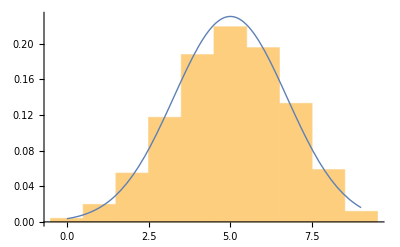
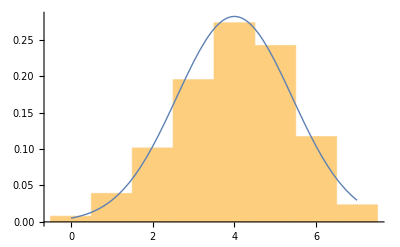
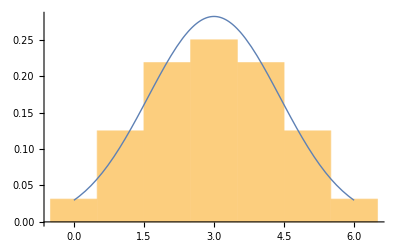
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
weightsDistribHistorgram/@(computeW/@ANew)
```

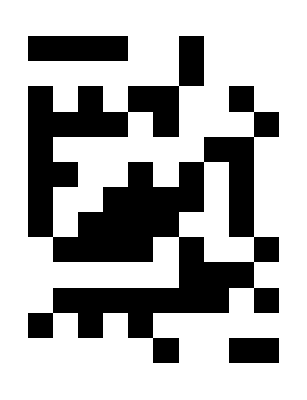
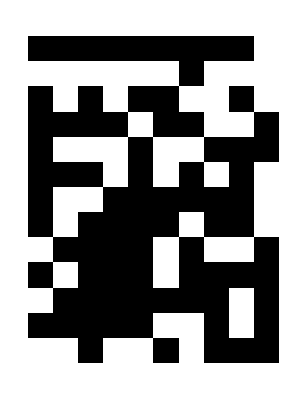
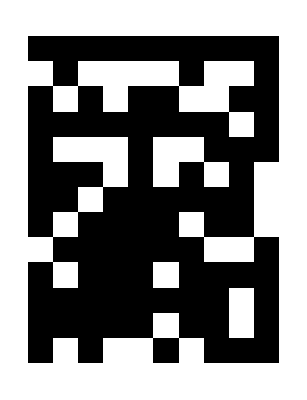
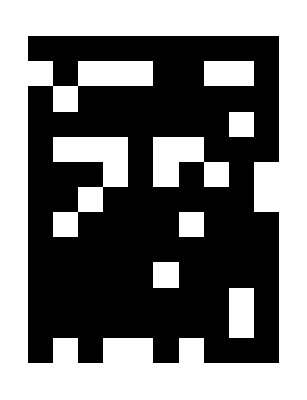
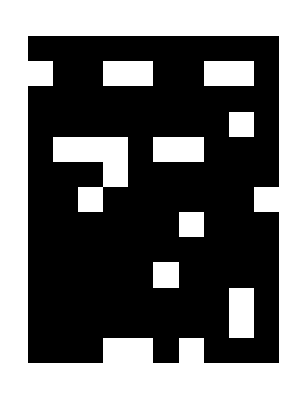
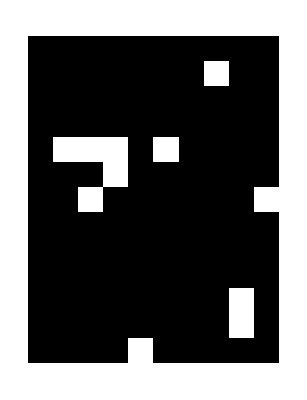

```mathematica
ANew=NestList[Map[ToPValue[#,1,0.3]&,#,{2}]&,A,5];
ArrayPlot/@ANew
```

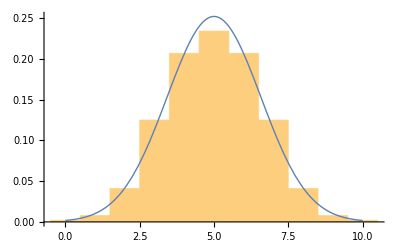
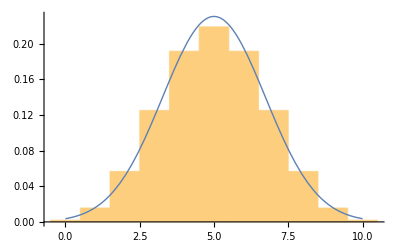
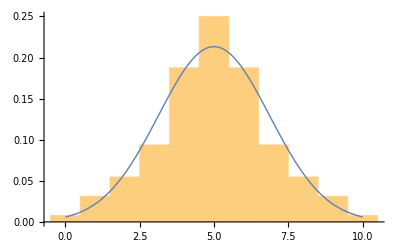
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
weightsDistribHistorgram/@(computeW/@ANew)
```

Nothing interesting.

```mathematica
Lets add CellularAutomaton
```

```mathematica
cellA=CellularAutomaton[#,{{1},0},13]&/@Range[50,60];
GraphicsGrid[Partition[ArrayPlot/@cellA,5]]
```

-Graphics-

```mathematica
cw=computeW/@cellA;
```

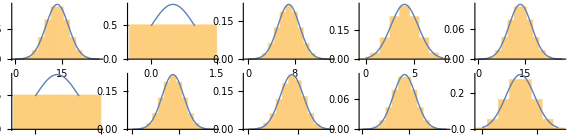

```mathematica
GraphicsGrid[Partition[weightsDistribHistorgram/@cw,5]]
```

```mathematica
ANew=NestList[Map[ToPValue[#,0,0.3]&,#,{2}]&,cellA[[1]],7];
```

```mathematica
ArrayPlot/@ANew
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

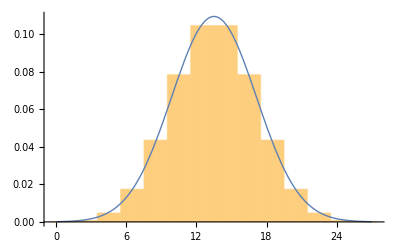
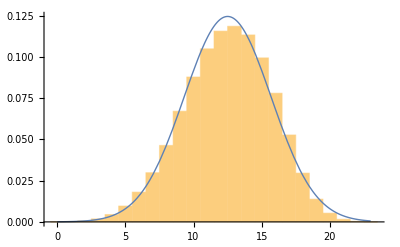
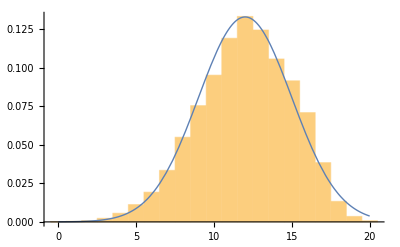
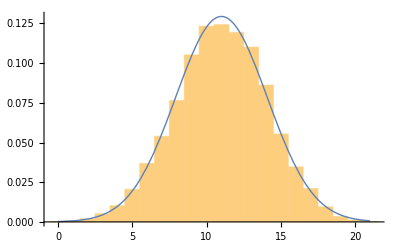
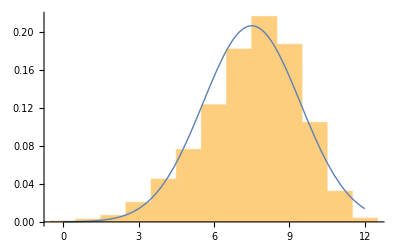
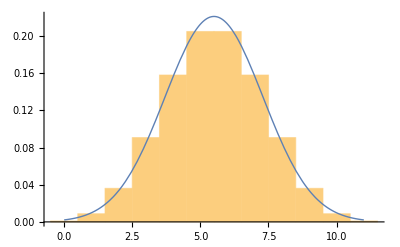
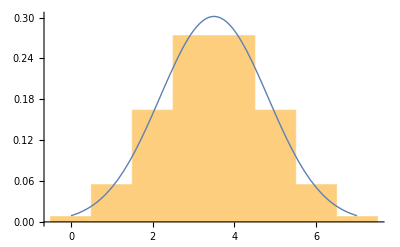
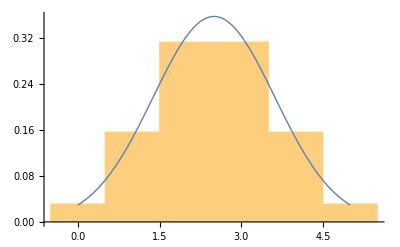

```mathematica
weightsDistribHistorgram/@(computeW/@ANew)
```

Good. We get not a Normal Distribution using cell auto basis.

```mathematica
Map-Reduce method
```

Now lets make classic parallelization using Map-Reduce method. Let see on computeW function:

```mathematica
computeW[a_]:=Module[{ad,b,genAD,weights},
ad=FromDigits[#,2]&/@a;
b=Tuples[{0,1},a//Length];
genAD=Fold[BitXor]/@((Times[ad,#]&)/@b)//Union;
weights= 𝒲D/@genAD;
weights//Tally
]
```

```mathematica
computeW2[a_]:=Module[{ad,b1,b2,genAD,genAD2,weights,weights2},
ad=FromDigits[#,2]&/@a;
b1=Join[{0},#]&/@Tuples[{0,1},(a//Length)-1];
b2=Join[{1},#]&/@Tuples[{0,1},(a//Length)-1];

genAD=Fold[BitXor]/@((Times[ad,#]&)/@b1)//Union;
genAD2=Fold[BitXor]/@((Times[ad,#]&)/@b2)//Union;

weights= 𝒲D/@genAD;
weights2= 𝒲D/@genAD2;

{{genAD,weights},{genAD2,weights2}}
]
```

```mathematica
A=RandomChoice[{0,1},{7,6}]
w=computeW2[A]
```

{{0,1,0,1,0,0},{1,0,0,1,0,1},{0,0,0,0,0,0},{0,0,1,1,0,1},{0,0,1,1,1,1},{0,0,1,0,1,0},{1,0,1,0,1,0}}

{{{0,2,5,7,8,10,13,15,32,34,37,39,40,42,45,47},{0,1,2,3,1,2,3,4,1,2,3,4,2,3,4,5}},{{17,19,20,22,25,27,28,30,49,51,52,54,57,59,60,62},{2,3,2,3,3,4,3,4,3,4,3,4,4,5,4,5}}}

```mathematica
A=RandomChoice[{0,1},{7,6}]
w=computeW2[A]
```

{{0,0,0,1,0,0},{1,0,1,1,0,0},{1,1,1,1,1,1},{0,1,0,1,1,1},{1,1,1,1,1,1},{1,0,0,0,0,0},{1,1,1,1,1,1}}

{{{0,4,8,12,19,23,27,31,32,36,40,44,51,55,59,63},{0,1,1,2,3,4,4,5,1,2,2,3,4,5,5,6}},{{0,4,8,12,19,23,27,31,32,36,40,44,51,55,59,63},{0,1,1,2,3,4,4,5,1,2,2,3,4,5,5,6}}}

```mathematica
Reduce detail in Map-Reduce.
```

We have to work with XOR-linear independence basis vectors to make map-reduce effective. The last example shows us that we have to join weights checking if numbers(vectors) are not the same.

```mathematica
(*In our case it will be useful to calc only basic vectors and find their WEIGHTS on the last step*)
mergeW2[gen1_,gen2_]:=Module[{gen,w},
gen=gen1[[1]]~Join~gen2[[1]]//Union;
{gen,𝒲D/@gen}
]
mergeW2[w[[1]],w[[2]]]
```

{{0,4,8,12,19,23,27,31,32,36,40,44,51,55,59,63},{0,1,1,2,3,4,4,5,1,2,2,3,4,5,5,6}}

FIX: to fix w recalculation

ComputeW function have to work with any basis vectors prefix. Not only {0} or {1}

```mathematica
computeWpre[a_,prefix_:{}]:=Module[{l=Length@prefix,lneed=Length@a,b={},times={},time=0,genAD={},w={},ad},
ad=FromDigits[#,2]&/@a;
b=Join[prefix,#]&/@Tuples[{0,1},lneed-l];
genAD=Map[Fold[BitXor],Map[Times[ad,#]&,b]];
genAD=genAD//Union//Sort;
w=𝒲D/@genAD;
{genAD,w}
]
A=RandomChoice[{0,1},{7,6}];
computeWpre[A] ==(computeWpre[A,{1}]~mergeW2~computeWpre[A,{0}])
```

True

```mathematica
bPrefixs=Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

{{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63},{0,1,1,2,1,2,2,3,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,5,3,4,4,5,4,5,5,6}}

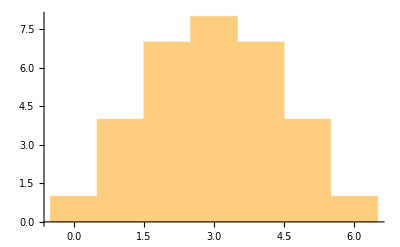

```mathematica
{numbers,w}=Fold[mergeW2][Parallelize[computeWpre[A,#]&/@bPrefixs]]
Histogram@w
```

We used Parallelize to compute basis vectors with prefix on independent nodes (if possible).

```mathematica
Parallelize Map-Reduce
```

```mathematica
computeParallelMapReduce[fmap_,freduce_,data_,prefix_:{{}}]:=
Fold[freduce,
Parallelize[Map[fmap[data,#]&,prefix]]
]
```

```mathematica
computeParallelMapReduce[computeWpre,mergeW2,A,bPrefixs]
```

{{0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63},{0,1,1,2,1,2,2,3,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,5,3,4,4,5,4,5,5,6}}

```mathematica
computeParallelMapReduce[computeWpre,mergeW2,{{}}]
```

{{0},{0}}

If there is any computational acceleration in such realization?

```mathematica
times={};
For[i=1,i<10,i++,
time={};
A=RandomChoice[{0,1},{9+i,5+i}]//Union;
res=computeW[A]//AbsoluteTiming;
time=AppendTo[time,res[[1]]];
res=computeParallelMapReduce[computeWpre,mergeW2,A,bPrefixs]//AbsoluteTiming;
time=AppendTo[time,res[[1]]];
times=AppendTo[times,time];
(*Print[i];*)
]
```

```mathematica
ListLinePlot[times//Transpose,PlotRange->All,PlotLabels->{"one core","parallel"}]
```

-Graphics-

Our parallel implementation using left fold and merging is slower then “one core” computeW. FIX in the future.
To optimise we need to make linear-xor independent basis and then parallize the computing without mention same numbers at different Map executions.

```mathematica
Reading input file
```

```mathematica
fileIn="E:\\data\\in.txt";
fileOut="E:\\data\\out.txt"

dataStr=ReadList[fileIn,String]
A=(Interpreter["Number"]/@Characters@#&)/@dataStr
```

E:\data\out.txt

{000101,010100,110000,111000}

{{0,0,0,1,0,1},{0,1,0,1,0,0},{1,1,0,0,0,0},{1,1,1,0,0,0}}

{{0,1},{2,6},{1,1},{3,6},{4,1},{5,1}}

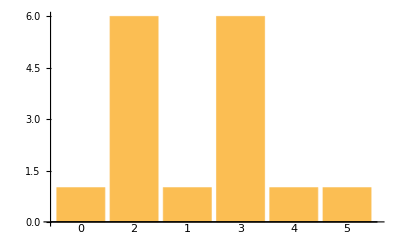

```mathematica
w=computeW[A]
weightsHistorgram@w
```

```mathematica
w=SortBy[w,Last]//Reverse
```

{{3,6},{2,6},{5,1},{4,1},{1,1},{0,1}}

```mathematica
stream=OpenWrite[fileOut];
WriteString[stream,StringTemplate["`w`\t`freq`\n"][ <|"w"->#[[1]],"freq"->#[[2]]|> ]]&/@w;
Close[fileOut]
```

E:\data\out.txt

```mathematica
ReadList[fileOut,String]
```

{3	6,2	6,5	1,4	1,1	1,0	1}

```mathematica
One page code
```

```mathematica
fileIn="E:\\data\\in.txt";
fileOut="E:\\data\\out.txt";

dataStr=ReadList[fileIn,String];
A=(Interpreter["Number"]/@Characters@#&)/@dataStr;

𝒲D=DigitCount[#,2,1]&;
computeW[a_]:=Module[{ad,b,genAD,weights},
ad=FromDigits[#,2]&/@a;
b=Tuples[{0,1},a//Length];
genAD=Fold[BitXor]/@((Times[ad,#]&)/@b)//Union;
weights= 𝒲D/@genAD;
weights//Tally
]

w=computeW[A];
w=SortBy[w,Last]//Reverse;

stream=OpenWrite[fileOut];
WriteString[stream,StringTemplate["`w`\t`freq`\n"][ <|"w"->#[[1]],"freq"->#[[2]]|> ]]&/@w;
Close[fileOut]
```

E:\data\out.txt

```mathematica
THE END
```

Optimization

1) Find xor-linear independent basis of A and use it instead of A.

2) Don’t use Fold in parallel version.

3) Reduce function in Map-Reduce have to know that we used independent basis.

4) If we have input basis with lot of “0” and few “1” we need to migrate to sparse arrays usage.
 

Algorithmic complexity

Let the source basis A is xor-linear independent and have K vectors with size N.
B have 2^K vectors.

Fair BitXor have O(N) comlexity .

The most complex function is:
genAD=Fold[BitXor]/@((Times[ad,#]&)/@b);

  have O ( (K*N)*(2^K * N) ) complexity which equal to O(N^2 * K * 2^K)
Fine parallel version with P independent nodes will works at O(N^2 * K * 2^K* (log(P)/ P)).

If vector size is constant then N^2 is a constant C. Result complexity = O(K*2^K).
If vector basis size is constant then K is a constant C. Result complexity = O(N^2).